```mathematica
SetDirectory[NotebookDirectory[]];
```

## This explains the method: http://math.stackexchange.com/questions/628681/how-to-compute-moments-of-log-normal-distribution

### Mean

```mathematica
Mean[LogNormalDistribution[μ,σ]]
```

ⅇ^(μ+σ^2/2)

### Variance

```mathematica
Variance[LogNormalDistribution[μ,σ]]
```

ⅇ^(2 μ+σ^2) (-1+ⅇ^(σ^2))

## The performance of a particular type of derivative is given by the following formula

### Transformed distribution

```mathematica
Mean[TransformedDistribution[S^2,S\[Distributed]LogNormalDistribution[μ,σ]]]
```

ⅇ^(2 μ+2 σ^2)

### Alternative derivative

```mathematica
Mean@ParameterMixtureDistribution[NormalDistribution[p^2,1], p \[Distributed] LogNormalDistribution[μ,σ]]
```

ⅇ^(2 (μ+σ^2))

## Generating data and estimating via MM

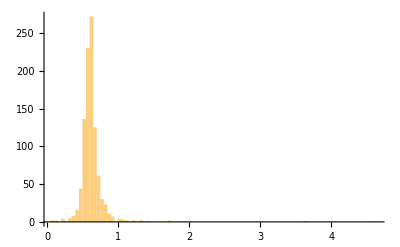

```mathematica
data = RandomVariate[TransformedDistribution[Exp[S],S \[Distributed] StudentTDistribution[-0.5,0.1,2]],{1000}];
Histogram[data,100]
```

```mathematica
Clear[μ,σ]
{μ,σ}={NSolve[{Mean[data]==Mean[LogNormalDistribution[μ,σ]],Variance[data]==Variance[LogNormalDistribution[μ,σ]],σ>0},{μ,σ},Reals][[1,1,2]],NSolve[{Mean[data]==Mean[LogNormalDistribution[μ,σ]],Variance[data]==Variance[LogNormalDistribution[μ,σ]],σ>0},{μ,σ},Reals][[1,2,2]]}
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{-0.517722,0.331441}

### Compare the estimated model with the data.

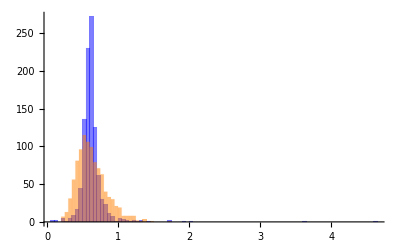

```mathematica
Histogram[{data,RandomVariate[LogNormalDistribution[μ,σ],{1000}]},100,ChartStyle->{Blue,Orange}]
```